```mathematica
<<peeters`

(*relative to ~/physicsplay*)
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

peeters`

/Users/pjoot/project/figures/GAelectrodynamics

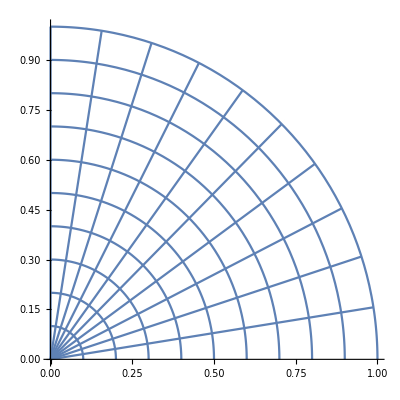

```mathematica
ClearAll[ toVector, polar, elliptical]

toVector[z_] := {z // Re, z //Im};

polar[r_, t_] := r Exp[I t] // toVector;

Module[{t1,t2,tm, range},
range = {{0,1},{0,1}};
t1 = Table[ParametricPlot[polar[r,t],{t,0,Pi/2}, PlotRange-> range],{r,0.1,1,0.1}] ;
tm = Pi/2;
t2 = Table[ParametricPlot[polar[r,t],{r,0,1}, PlotRange->range],{t,0.1tm,tm,0.1tm}] ;
Show[t1,t2]
]
```

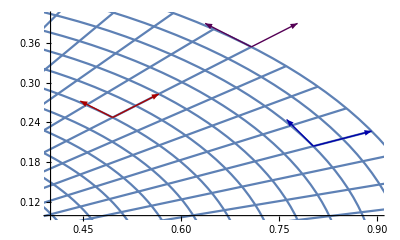

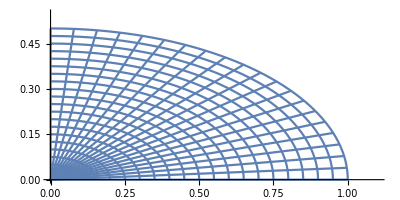

```mathematica
ClearAll[  elliptical, ellipticalH ]

elliptical[a_, b_,t_] :=  Module[{m},
m = ArcTanh[b/a];
a Cosh[m+ I t]/Cosh[m] // toVector];

drEllipticalH[a_,t_] :=  Module[{m},
m = ArcTanh[1/2];
 Cosh[m+ I t]/Cosh[m] // toVector];
dtEllipticalH[a_,t_] :=  Module[{m},
m = ArcTanh[1/2];
 a I Sinh[m+ I t]/Cosh[m] // toVector];
ellipticalH[a_,t_] := a drEllipticalH[a,t];

p2 = Module[{t1,t2,tm,range, p1, rp1, tp1, g, dr1, dt1, p2, rp2, tp2, da, rp3, tp3, p3, dr3, dt3},
(*range =1.1 {{0,1},{0,1}};*)
range = {{0.4,0.9},{0.1,0.4}};
tm = Pi/2;
da = 0.1;

t1 = Table[ParametricPlot[ellipticalH[r,t],{t,0,tm}, PlotRange->range],{r,0.1,1,0.05}] ;
t2 = Table[ParametricPlot[ellipticalH[r,t],{r,0,1}, PlotRange->range],{t,0,tm,0.05tm}] ;
rp1 = 0.7;
tp1 = 5 Pi/20;
p1 = ellipticalH[rp1, tp1];
dr1 = da drEllipticalH[rp1, tp1];
dt1 = da dtEllipticalH[rp1, tp1];

rp2 = 0.9;
tp2 = 3 Pi/20;
p2 = ellipticalH[rp2, tp2];
dr2 = da drEllipticalH[rp2, tp2];
dt2 = da dtEllipticalH[rp2, tp2];

rp3=1.0;
tp3 = 5 Pi/20;
p3=ellipticalH[rp3,tp3];
dr3=da drEllipticalH[rp3,tp3];
dt3=da dtEllipticalH[rp3,tp3];

g =Graphics[{
Red//Darker,
Thick,
Arrow[{p1, p1+dr1}],
Arrow[{p1, p1 + dt1}],
Blue//Darker,
Arrow[{p2, p2+dr2}],
Arrow[{p2, p2 + dt2}],
Purple//Darker,
Arrow[{p3,p3+dr3}],
Arrow[{p3,p3+dt3}]
}];
Show[t1,t2, g]
]

p1 = Module[{t1,t2,tm,range, p1, rp1, tp1, g, dr1, dt1, p2, rp2, tp2, da, rp3, tp3, p3, dr3, dt3},
range =1.1 {{0,1},{0,0.5}};

tm = Pi/2;
da = 0.1;

t1 = Table[ParametricPlot[ellipticalH[r,t],{t,0,tm}, PlotRange->range],{r,0.05,1,0.05}] ;
t2 = Table[ParametricPlot[ellipticalH[r,t],{r,0,1}, PlotRange->range],{t,0,tm,0.05tm}] ;

Show[t1,t2]
]
```

```mathematica
peeters`exportForLatex["ellipticalContoursFig1", p1]
peeters`exportForLatex["ellipticalContoursFig2", p2]
```

{ellipticalContoursFig1.eps,ellipticalContoursFig1pn.png}

{ellipticalContoursFig2.eps,ellipticalContoursFig2pn.png}